```mathematica
Needs["Screening`",NotebookDirectory[]<>"../packages/Screening.wl"]
(*Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]*)
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
```

#### Get potential outside earth

```mathematica
(*ϕtest=Quiet@Screening`GetScreenedϕ[0.05,PowerRange[1/20,4,1+2/10]];*)
ϕtest=Quiet@Screening`GetScreenedϕ[0.05];
```

1

Zooming In

2

3

4

5

6

7

8

9

10

11

12

13

Reached Earth phi

```mathematica
(*Plot[ϕtest["ϕ(r)"][x],{x,ϕtest["rE"],1},PlotStyle->Red]*)
```

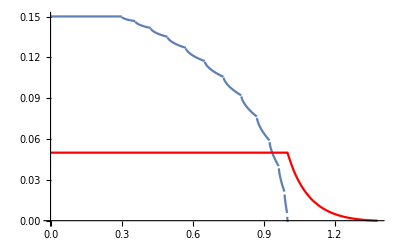

```mathematica
Show[{Plot[betaSolver[ϕtest,r ϕtest["rE"]],{r,0,1},PlotRange->All],
Plot[If[r>1,ϕtest["ϕ(r)"][r ϕtest["rE"]],ϕtest["ϕE"]],{r,0,1/ϕtest["rE"]},PlotStyle->Red]}]
```

#### solver for β

figure out how to translate this into Ncharge with actual units etc .

```mathematica
(*betaSolver[phiE_,RMaxList_,r_]:=
(*Use to solve for overall charge density in the Earth as a function of radius. Subscript[n, H] - Subscript[n, e] = Subscript[α, H]* β(r) * (Subscript[n, H]^F + Subscript[n, e]^F)*)
Module[{j = Length[RMaxList]},-Sum[rootF[i,RMaxList[[i,1]],r,phiE,j],{i,1,j}]];*)
```

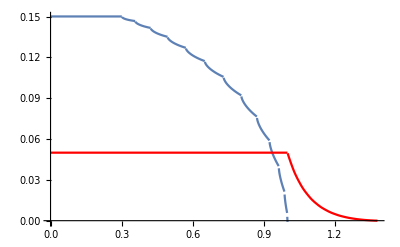

```mathematica
Show[{Plot[betaSolver[ϕtest,r ϕtest["rE"]],{r,0,1},PlotRange->All],
Plot[If[r>1,ϕtest["ϕ(r)"][r ϕtest["rE"]],ϕtest["ϕE"]],{r,0,1/ϕtest["rE"]},PlotStyle->Red]}]
```

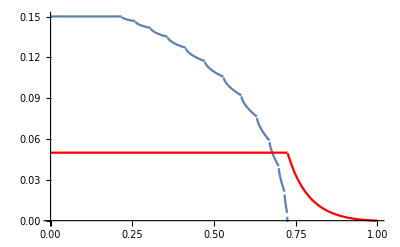

```mathematica
Show[{Plot[betaSolver[ϕtest,r],{r,0,ϕtest["rE"]},PlotRange->All],
Plot[If[r>ϕtest["rE"],ϕtest["ϕ(r)"][r],ϕtest["ϕE"]],{r,0,1},PlotStyle->Red]}]
```

```mathematica
"n_H - n_e = α_H* β(r) * (n_H^F + n_e^F)

α_H(n_H^F + n_e^F) = n_H^F
";
```

```mathematica
"Interesting! So a this corresponds to a 15% "
```

```mathematica
"GeV dark proton and light dark electron with 5% mass fraction of total DM"
Capture`naDM[0.05,"m"2 10^3/.SIConstRepl] m^-3
"Earth's volume is"
(4 π)/3("rE")^3 m^3/.EarthRepl
(*"So assuming the total captured number is given by the integral over the above"*)
(*Out[-4]Out[-2]*)
```

GeV dark proton and light dark electron with 5% mass fraction of total DM

14654.2/m^3

Earth's volume is

1.08321×10^21 m^3

```mathematica
"Assuming neutrality, the flowing number in the Earth is given by 2 times total number at infinity times the overdensity due to the escape velocity, we can ignore gravity for now and just take it to be two time aDM at infinity"
```

```mathematica
"So the value we want is"
(4 π)/3(∫_0)^rE ⅆr r^2 β(r)
```

So the value we want is

we'll need to interpolate over the beta solution

InterpolatingFunction[…]

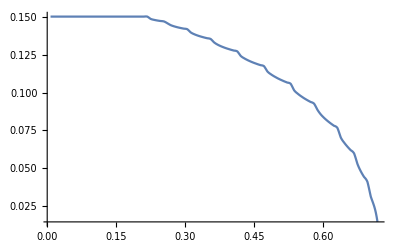

```mathematica
(*"we'll need to interpolate over the beta solution "
Table[{r,betaSolver[ϕtest,r]},{r,ϕtest["rE"]/#,ϕtest["rE"]-ϕtest["rE"]/#,ϕtest["rE"]/#}]&[100];
Interpolation[%]
Plot[%[r],{r,%["Domain"][[1,1]],%["Domain"][[1,2]]}]*)
```

InterpolatingFunction[…]

-Graphics-

2.90031×10^27 2^(5-logm) 5^(6-logm)

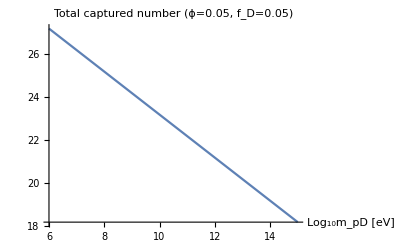

3.62539×10^23

```mathematica
βrfunctest = Getβrfunc[ϕtest,100]
Plot[βrfunctest[r],{r,βrfunctest["Domain"][[1,1]],βrfunctest["Domain"][[1,2]]}]
(Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3)(4 π(("rE")/(βrfunctest["Domain"][[1,2]]))^3 m^3/.Constants`EarthRepl)NIntegrate[r^2 βrfunctest[r],{r,βrfunctest["Domain"][[1,1]],βrfunctest["Domain"][[1,2]]}](*logm = 0 gives 1 MeV dark proton*)
Plot[Log10@%,{logm,6,15},PlotLabel->"Total captured number (ϕ=0.05, f_D=0.05)",AxesLabel->{"Log_10m_pD [eV]"}]
Out[-2]/.logm->Log10[4]+ 9
```

```mathematica
"We should turn this into a density / contour plot as a function of ϕ and m_pD"
"we'll want a to wrap the whole thing into a module too"
```

We should turn this into a density / contour plot as a function of ϕ and m_pD

we'll want a to wrap the whole thing into a module too

```mathematica
"Also, why is there no dependence on α_D? Ah because this assumes that the debeye length is 0, and that contains both the temperature in the mirror sector and α_D"
"There is however, temperature / v_0 dependence in the conversion of ϕ -> vesc as well"
```

Also, why is there no dependence on α_D? Ah because this assumes that the debeye length is 0, and that contains both the temperature in the mirror sector and α_D

There is however, temperature / v_0 dependence in the conversion of ϕ -> vesc as well

```mathematica
βrfunctest = Getβrfunc[ϕtest,100]
Plot[βrfunctest[r],{r,βrfunctest["Domain"][[1,1]],βrfunctest["Domain"][[1,2]]}]
(Capture`naDM[0.05,"m"2 10^(logm-6)/.SIConstRepl] m^-3)(4 π(("rE")/(βrfunctest["Domain"][[1,2]]))^3 m^3/.Constants`EarthRepl)NIntegrate[r^2 βrfunctest[r],{r,βrfunctest["Domain"][[1,1]],βrfunctest["Domain"][[1,2]]}](*logm = 0 gives 1 MeV dark proton*)
Plot[Log10@%,{logm,6,15},PlotLabel->"Total captured number (ϕ=0.05, f_D=0.05)",AxesLabel->{"Log_10m_pD [eV]"}]
Out[-2]/.logm->Log10[4]+ 9
```

InterpolatingFunction[…]

-Graphics-

2.90031×10^27 2^(5-logm) 5^(6-logm)

-Graphics-

3.62539×10^23

```mathematica
GetTotalCapturedNtemp[ϕDict_,mDMtot_:"m"2 10^(logm-6)/.SIConstRepl,fD_:0.05]:=Module[{n∞aDM,βofr,βdom},

n∞aDM=(Capture`naDM[fD,mDMtot] m^-3);

βofr = ϕDict["β(r)"];
βdom = βofr["Domain"];
n∞aDM(4 π(("rE")/βdom[[1,2]])^3 m^3/.Constants`EarthRepl)NIntegrate[r^2 βofr[r],{r,βdom[[1,1]],βdom[[1,2]]}]
]
```

```mathematica
GetTotalCapturedNtemp[ϕtest]
```

2.90031×10^27 2^(5-logm) 5^(6-logm)

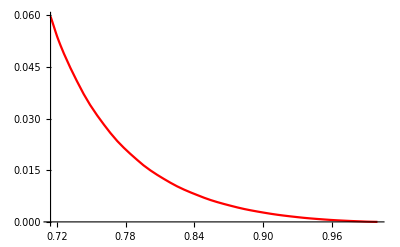

```mathematica
ϕdict = Block[{Print},Quiet@Screening`GetScreenedϕ[0.06]];
Plot[ϕdict["ϕ(r)"][x],{x,ϕdict["rE"],1},PlotStyle->Red]
```

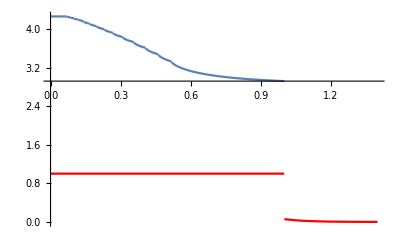

```mathematica
ϕdict = Block[{Print},Quiet@Screening`GetScreenedϕ[1]];
Show[{Plot[betaSolver[ϕdict,r ϕdict["rE"]],{r,0,1},PlotRange->All],
Plot[If[r>1,ϕdict["ϕ(r)"][r ϕdict["rE"]],ϕdict["ϕE"]],{r,0,1/ϕdict["rE"]},PlotStyle->Red]}]
```

```mathematica
"can we solve for beta even when the ϕ solution fails?"
```

```mathematica
ϕsolTable=Table[Block[{Print},Quiet@Screening`GetScreenedϕ[0.05 10^logϕ]],{logϕ, -5,0}];
```

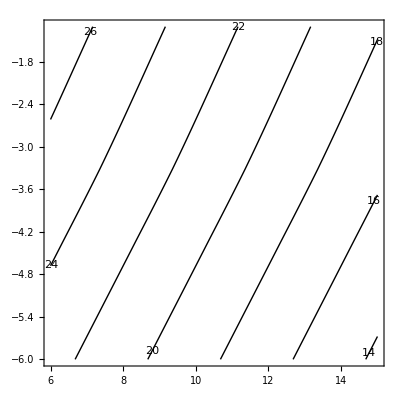

```mathematica
{Log10@#["ϕE"],Log10[ GetTotalCapturedN[#]/(2^(5-logm) 5^(6-logm))//Simplify]}&/@ϕsolTable;
Log10[2^(5-logm) 5^(6-logm)]+Interpolation[%][ϕE];
ContourPlot[%,{logm,6,15},{ϕE,-6,Log10[0.05]},ContourShading->None,ContourLabels->True,PlotRange->All]
```

#### Labeled plots of N_c and β

```mathematica
ϕsolTable=Table[Block[{Print},Quiet@Screening`GetScreenedϕ[0.05 10^logϕ]],{logϕ, -5,0}];
```

Log[2^(5-logm) 5^(6-logm)]/Log[10]+InterpolatingFunction[…][ϕE]

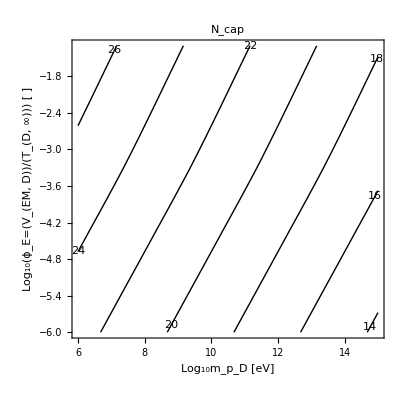

```mathematica
Nfunctest=Log10[2^(5-logm) 5^(6-logm)]+Interpolation[{Log10@#["ϕE"],Log10[ GetTotalCapturedN[#]/(2^(5-"logm") 5^(6-"logm"))//Simplify]}&/@ϕsolTable][ϕE]
ContourPlot[Nfunctest,{logm,6,15},{ϕE,-6,Log10[0.05]},ContourShading->None,ContourLabels->True,PlotRange->All,PlotLabel->"N_cap",FrameLabel->{"Log_10m_p_D [eV]","Log_10(ϕ_E=(V_(EM, D))/(T_(D, ∞))) [ ]"}]
```

InterpolatingFunction[…]

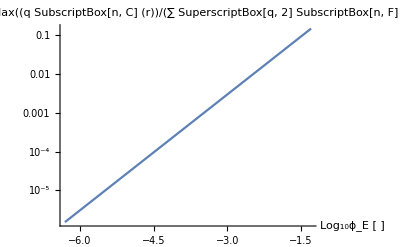

```mathematica
Interpolation[{Log10@#["ϕE"],Log10[ #["βmax"]]}&/@ϕsolTable]
LogPlot[10^(%[ϕE]),{ϕE,-6.3,-1.3},PlotLabel->"β_max = Max((q SubscriptBox[n, C] (r))/(∑ SuperscriptBox[q, 2] SubscriptBox[n, F] (r)))",AxesLabel->{"Log_10ϕ_E [ ]"}]
```

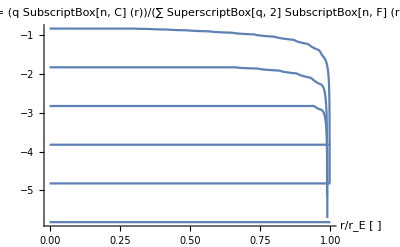

```mathematica
(*ϕsolTable=Table[Block[{Print},Quiet@Screening`GetScreenedϕ[0.05 10^logϕ]],{logϕ, -5,0}];*)
Quiet@Show[Table[Plot[Log10@ϕsolTable[[i]]["β(r)"][r ϕsolTable[[i]]["rE"] ],{r,0,1},PlotRange->All,PlotLabel->"β(r) = (q SubscriptBox[n, C] (r))/(∑ SuperscriptBox[q, 2] SubscriptBox[n, F] (r))",AxesLabel->{"r/r_E [ ]"}],{i,Length[ϕsolTable]}]]
```

#### v0 to vesc

Given a value of v0 and ϕ we want the corresponding vesc.

```mathematica
"We know"
(*(√3)/2*){"veDmean","vpDmean"}/.v0toβD[220 kmpers,meD,2000meD]//PowerExpand//Simplify//N
(%^-1 .%^-1)//PowerExpand//Simplify
√(2(("veDmean")^-2+("vpDmean")^-2)^-1)/.v0toβD[220 kmpers,meD,2000meD]//PowerExpand//Simplify//N
```

We know

{6958.75 kmpers,155.602 kmpers}

0.0000413223/kmpers^2

220. kmpers

```mathematica
Block[{βD,vpDmean,veDmean},
βD = 6/((meD + mpD)v0^2);
vpDmean = Sqrt[3/(mpD βD)];
veDmean = Sqrt[3/(meD βD)];
√(2(vpDmean^-2+veDmean^-2)^-1)//Simplify//PowerExpand
]
```

v0

```mathematica
Block[{ϕ,vesc,v0,q},
v0 = 220 kmpers;
ϕ = (-3 vesc^2)/(2 q v0^2);
Solve[ϕ==ϕE,vesc][[2]]/.ϕE->0.05
]
```

{vesc→(0.+40.1663 ⅈ) kmpers √q}

I think Start by doing a run with ϕE = 0.05, the boundary of the strong capture regime. 

Also I think for the capture code all we need is the potential at the earth. Once we have that

```mathematica
Block[{ϕE,vesc,v0,,v0s,q},
v0 = 220 kmpers;
(*ϕ = (-3 vesc^2)/(2 q "veDmean");*)
ϕE = 0.05;

v0s ={{"veDmean",-1},{"vpDmean",1}}/. v0toβD[v0,meD/.meD->mpD 10^-4,mpD]//PowerExpand;

Print[N@((("vesc")/10^3)^2)/.EarthRepl];
vescsq = -2/3#2ϕE #1^2 &[Sequence@@#]&/@v0s
(*Solve[ϕ==ϕE,vesc][[2]]/.ϕE->0.05*)
]
```

125.44

{8.06747×10^6 kmpers^2,-806.747 kmpers^2}

```mathematica
#1 #2&[Sequence@@#]&/@{{a,d},{b,c}}
```

{a d,b c}

#### maximum ϕE

```mathematica
"Solve for the maximum ϕE such that the escape velocity is real for qD > 0"
Solve[0==1/2 vescg^2+ -2/3 qD ϕE vbar^2,ϕE][[1]]
"We can restrict ϕE < the above (at least for now) so that vesc is real"
ϕE/.%%/.vescg->("vesc"/.EarthRepl)/.qD->1/.vbar -> 220 10^3//N
ϕE/.%%%/.vescg->("vesc"/.EarthRepl)/.qD->1/.vbar -> 20 10^3//N
(*vescg^2+ -2/3 qD ϕE vbar^2/.vescg->("vesc"/.EarthRepl)/.qD->1/.vbar -> 220 10^3/.ϕE->0.003887603305785124//N
vescg^2+ -2/3 qD ϕE vbar^2/.vescg->("vesc"/.EarthRepl)/.qD->1/.vbar -> 20 10^3/.ϕE->0.4704//N*)
```

Solve for the maximum ϕE such that the escape velocity is real for qD > 0

{ϕE→(3 vescg^2)/(4 qD vbar^2)}

We can restrict ϕE < the above (at least for now) so that vesc is real

0.0019438

0.2352

```mathematica
Veff["rE"/.EarthRepl,ϕE,qD,vbar]
```

-6.272×10^7+2/3 qD vbar^2 ϕE

#### Comparing extrema of 1D effective potential to the potential at Earth

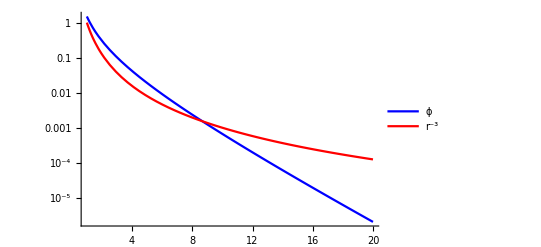

```mathematica
(*L^2/m/.repl
r^3 Abs@D[q ϕ[r],r]/.repl/.r->1//N*)
Legended[LogPlot[(*Abs[q ϕ[r]]/.repl*){Abs[q ϕ'[r]]/.repl,r^-3},{r,1,10 λ/.repl},PlotRange->All,PlotStyle->{Blue,Red}],LineLegend[{Blue,Red},{"ϕ","r^-3"}]]
```

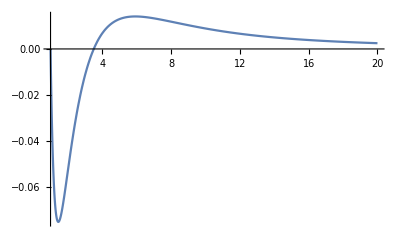

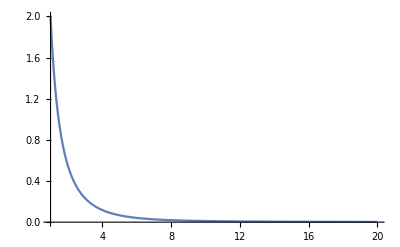

```mathematica
repl={ϕE->1,L->1,m->1/2,rE->1,λ->2,q->-1};
ϕ[r_]:=ϕE (rE E^(-(r-rE)/λ))/r
Veff[r_]:=L^2/(2 m r^2)+q ϕ[r]
Plot[Veff[r]/.repl,{r,1,10 λ/.repl},PlotRange->All]
Plot[Veff[r]/.q->1/.repl,{r,1,10 λ/.repl},PlotRange->All]
```

```mathematica
Veff[1]/.repl
ϕ[1]/.repl
```

0.125

1

```mathematica
Veff'[1]
```

1/2

```mathematica
Solve[Veff'[r]==0,r]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-L^2/(m r^3)-(ⅇ^(-(r-rE)/λ) q ϕE)/r^2-(ⅇ^(-(r-rE)/λ) q ϕE)/(r λ)==0,r]

```mathematica
D[q ϕ[r],r]
```

-(ⅇ^(-(r-rE)/λ) q ϕE)/r^2-(ⅇ^(-(r-rE)/λ) q ϕE)/(r λ)

```mathematica
"Potential for a monotonically decreasing in r, and strictly negative electrostatic potential ϕ with ϕ(r_E)= ϕ_E and q<0 (q below denotes |q|)"
potmonom=L^2/(2 m r^2)-q ϕE(rE/r)^n
"Now look for extrema"
D[potmonom,r]
%r^3//Simplify
Solve[%==0,r]
"So the value of the potential at the extremum is"
potmonomatrsol=potmonom/.%%[[1]]//Simplify//PowerExpand//FullSimplify//PowerExpand
"Which implies this value is greater than "
(potmonomatrsol/(q ϕE^(-2/(-2+n))))^(1/(n/(-2+n)))//Simplify//PowerExpand
(*ϕextr=Solve[%==ϕE,ϕE]//Simplify
potmonom/.ϕextr[[1]]//Simplify
%//PowerExpand//Simplify*)
```

Potential for a monotonically decreasing in r, and strictly negative electrostatic potential ϕ with ϕ(r_E)= ϕ_E and q<0 (q below denotes |q|)

L^2/(2 m r^2)-q (rE/r)^n ϕE

Now look for extrema

-L^2/(m r^3)+(n q rE (rE/r)^(-1+n) ϕE)/r^2

-L^2/m+n q r^2 (rE/r)^n ϕE

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→((L^2 rE^-n)/(m n q ϕE))^(1/(2-n))}}

So the value of the potential at the extremum is

1/2 L^((2 n)/(-2+n)) m^(-n/(-2+n)) (n^(-2/(-2+n))-2 n^(-n/(-2+n))) q^(-2/(-2+n)) rE^(-(2 n)/(-2+n)) ϕE^(-2/(-2+n))

Which implies this value is greater than

(2^(-1+2/n) L^2 (n^(-2/(-2+n))-2 n^(-n/(-2+n)))^((-2+n)/n))/(m q rE^2)

```mathematica
(potmonom/.r->rE)/.q->1/.repl
```

-1/2

1/2 ⅇ^(2 Re[(n Log[L])/(-2+n)]+Re[(n Log[m])/(2-n)]-2 (Re[Log[q]/(-2+n)]+Re[(n Log[rE])/(-2+n)]+Re[Log[ϕE]/(-2+n)])) Abs[n^(-2/(-2+n))-2 n^(-n/(-2+n))]-Abs[L^2/(2 m rE^2)-q ϕE]

-1/2+1/2 Abs[n^(-2/(-2+n))-2 n^(-n/(-2+n))]

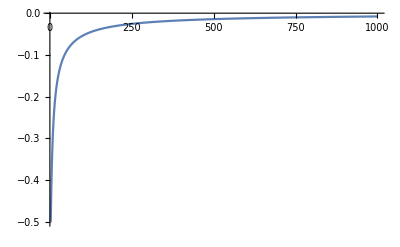

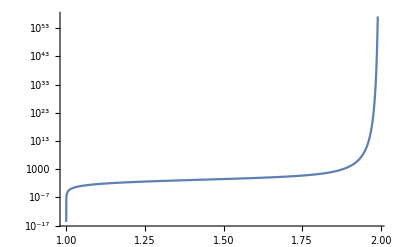

```mathematica
Abs@potmonomatrsol-Abs@(potmonom/.r->rE)//Simplify
%/.q->1/.repl
Plot[%,{n,2.01,1000},PlotRange->All]
LogPlot[%%,{n,1,1.99},PlotRange->All]
```

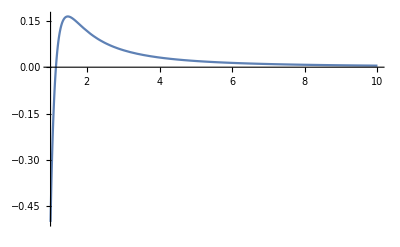

```mathematica
Plot[potmonom/.q->1/.repl/.n->7,{r,1,10},PlotRange->All]
```

```mathematica
D[(n^(-2/(-2+n))-2 n^(-n/(-2+n))),n]//Simplify
"So increases with n if n>2 otherwise decreases"
```

(2 n^(n/(2-n)) Log[n])/(-2+n)

So increases with n if n>2 otherwise decreases

{1/r^3,-1/r^4,-1/r^4+1/r^3}

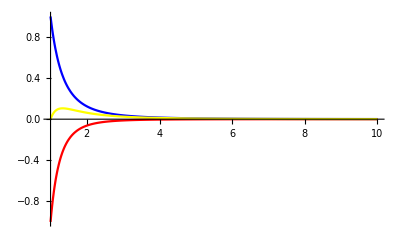

{1,-1,0}

```mathematica
{1/r^3,-1/r^n/.n->4,1/r^3-1/r^n/.n->4}
Plot[%,{r,1,10},PlotStyle->{Blue,Red,Yellow},PlotRange->All]
%%/.r->1
```

Both the ang term and the ϕ term have absolute values which are montonically decreasing in r. And since they have opposite signs

They

## Scrap

#### Test package

```mathematica
ϕtest=Screening`GetScreenedϕ[0.05,PowerRange[1/20,4,1+2/10]];
```

1

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

Zooming In

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

2

3

4

5

6

7

8

9

10

11

12

13

Reached Earth phi

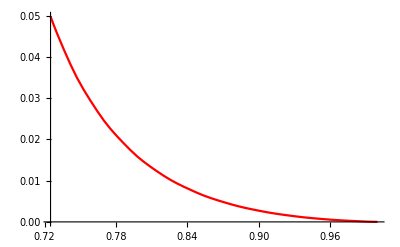

```mathematica
testCurrent=Plot[ϕtest["ϕ(r)"][x],{x,ϕtest["phiList"][[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```

#### From Ina’s code

This is a modularized version of Ina’s screening code

```mathematica
"We want to make sure we match on to this - the plot from the original version of the code."
```

We want to make sure we match on to this - the plot from the original version of the code.

```mathematica
f=Interpolation[phiList];
testCurrent=Plot[f[x],{x,phiList[[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```

-Graphics-

#### MB Distribution Case

```mathematica
(*N@vInfList 
"What are the units here? Is it relative to vesc? or v0?"*)
```

vInfList

What are the units here? Is it relative to vesc? or v0?

```mathematica
(**)
```

```mathematica
(*
derivF[i_,RMax_,r_,phi_?NumericQ,n_,vInfList_,RMaxList_,MBfactor_]:=
(*Used to find a good endpoint for solving the F[phi]=0 equation (there can be a superfluous root at higher phi)*)Re[N[(-3ⅇ^(-3phi)/2-3ⅇ^(3phi/2)/2)/n+((MBfactor/(2*√(vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]]))vInfList[[i]]))),20]];(*CHANGED*)

complexF[i_,RMax_,r_,vInfList_,RMaxList_]:=
(*find where the function F[phi] (where we are solving F[phi]=0 to find phi) goes complex, which will cause the root finding protocol to not work well*)
N[RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])-vInfList[[i]]^2,50];

rootF[i_,RMax_,r_,phi_?NumericQ,n_,vInfList_,RMaxList_,MBfactor_]:=

Re[N[(ⅇ^(-3phi/2)-ⅇ^(3phi/2))/n+MBfactor/vInfList[[i]] Sqrt[vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])],50]];(*CHANGED*)*)
```

```mathematica
(*Clear[GetScreenedϕ]
GetScreenedϕ[phiEarth_:0.05,vInfList_:PowerRange[1/20,4,1+2/10](*,pointNumber_:100*)]:=Module[{MBNorm,MBfactor,pointNumber=100,phiList={{1,0}},RMaxList={{1,0}},minPoint =SetPrecision[ 0.5,20],scanPoints,earthFlag,zoomFlag,phiListWorking,delNum,zoomCount,phiMin,phiMax,res,successplot,phiNew,phiFunc,ckplot,insertPoints,f},

(*pointNumber=100;*)(*keep pointnumber low for fast run times, ~100 works well*)
(*
vInfList - [v0] velocities at infinity being sampled
phiEarth - []
scanpoints - []
RMaxList - []
*)

MBNorm=SetPrecision[Sum[vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2],{i,1,Length[vInfList]}],20];
MBfactor[i_]:=SetPrecision[ vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2]/MBNorm,20];

(* start of recursion to scan over different r's to find escape potential *)
(*phiList={{1,0}};*)
(*RMaxList={{1,0}};*)
(*minPoint =SetPrecision[ 0.5,20];*)(*CHANGED*)
Clear[scanPoints];
scanPoints=SetPrecision[Table[1-i(1-minPoint)/pointNumber,{i,pointNumber}],20];
earthFlag=False (*triggers True when escape potential matches Earth potential*);
zoomFlag=False (*triggers True when the recursion zooms in to finer value of the radius*);
(*recursion over different values of v_inf*)
Do[
phiListWorking = {};
delNum=0;
zoomCount=0;
If[earthFlag,Break[]];
If[zoomFlag,Break[]];
Print[j];
(*recursion over different values of r*);
Do[
If[zoomCount>12,zoomFlag=True;Print["You've zoomed in more than 12 times, problem?"];
Break[]];

phiMin=Max[Table[complexF[l,RMaxList[[l,1]],scanPoints[[k]],vInfList,RMaxList],{l,j}]]+10^(-15);
Do[If[Sqrt[vInfList[[l]]^2+phiMin-RMaxList[[l,1]]^2/scanPoints[[k]]^2(vInfList[[l]]^2+RMaxList[[l,2]])]<=10^-8,
phiMin+=10^-12],
{l,j}];

phiMax=phi/.FindRoot[Sum[derivF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin,0.1},Method->"Brent"];

res=Check[FindRoot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],
{phi,phiMin-10^(-12),phiMax},
Method->"Brent",WorkingPrecision->20],$Failed[Evaluate@$MessageList],
FindRoot::bbrac];


If[
FreeQ[res,$Failed](*check whether FindRoot was succesful*),
successplot=Plot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin-10^(-12),phiMax}];(*ADDED*)
phiNew=phi/.res;
If[phiNew>phiEarth,(*CHANGED*)
earthFlag=True;phiList=Join[phiList,phiListWorking];Print["Reached Earth phi"];
Break[]];

(*make updated potential function so far*);
AppendTo[phiListWorking,{scanPoints[[k]],phiNew}];
phiFunc=Interpolation[Join[phiList,phiListWorking]];
delNum+=1;

(*check if we have hit RMax(v_inf)*);
If[phiFunc'[scanPoints[[k]]]*scanPoints[[k]]+2phiFunc[scanPoints[[k]]]+2(vInfList[[j+1]])^2<=0,AppendTo[RMaxList,{scanPoints[[k]],phiNew}];
phiList=Join[phiList,phiListWorking];
scanPoints=Drop[scanPoints,delNum];
pointNumber-=k;
Return[phiList[[-1]]];];,

(*if FindRoot was not succesful, go back a step in r and insert extra points to "fine-grain" your scan over r*)
Print["Zooming In"];
ckplot=Plot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin-10^(-12),phiMax}];(*ADDED*)
zoomCount+=1;
(*pick extra points to insert*);
If[k==1,insertPoints=Table[RMaxList[[j,1]]-(RMaxList[[j,1]]-scanPoints[[k]])/10 p,{p,0,9}],insertPoints=Table[scanPoints[[k-1]]+(scanPoints[[k]]-scanPoints[[k-1]])/10 p,{p,0,9}]];

scanPoints=Join[scanPoints[[1;;k-1]],insertPoints,scanPoints[[k;;]]];
pointNumber+=10;
delNum+=1
],

{k,10000}],
{j,1,Length[vInfList]-1}];


f=Interpolation[phiList];

<|"ϕ(r)"->f,"phiList"->phiList|>
]*)
```

```mathematica
(*ϕtest=GetScreenedϕ[0.05,PowerRange[1/20,4,1+2/10]];*)
```

1

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

Zooming In

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

2

3

4

5

6

7

8

9

10

11

12

13

Reached Earth phi

```mathematica
(*testCurrent=Plot[ϕtest["ϕ(r)"][x],{x,ϕtest["phiList"][[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]*)
```

-Graphics-